# Reálný trám

## dubový trám bez závaží

```mathematica
ClearAll["Global`*"]
Needs["NDSolve`FEM`"]
```

WolframAlphaQueryResults

scientific name | Quercus
material class | hardwood

```mathematica
(*zjistění potřebných parametrů*)
dens=650;
BeamLength= 10; 
BeamWidth = 0.25;
q=BeamWidth^2*dens*9.81;(*q=S*g*Rho=a^2*Rho*g*)
EE:= 11*10^9;
Izz=dens*BeamLength*BeamWidth^4/6;(*wikipedia->Izz=1/12*m*(sirka^2+vyska^2)*)
LoadDensity[X_]:=q
```

```mathematica
(*nyní řešíme dif. rci.*)
EulerBernoulliSolution = 
DSolve[
{
D[EE*Izz*D[y[X], X, X], X, X] == LoadDensity[X], 
y[-BeamLength/2]==0, 
y[BeamLength/2]==0, 
y'[-BeamLength/2]==0, 
y'[BeamLength/2]==0
}, 
y, 
X];
```

```mathematica
(*nyní přichází na řadu vykreslení (tedy vykradení notebooku pana Průši)*)
```

```mathematica
DisplacementEulerBernoulli[X_, Y_]:= {-Y*Sin[ArcTan[y'[X]]],y[X] + Y*(Cos[ArcTan[y'[X]]]-1)  }  /. EulerBernoulliSolution
u=Function[{X,Y},DisplacementEulerBernoulli[X, Y][[1]][[1]]]; 
v=Function[{X,Y},DisplacementEulerBernoulli[X, Y][[1]][[2]]]; 
BeamMesh = ToElementMesh[Rectangle[{-BeamLength/2, -BeamWidth/2}, {BeamLength/2, BeamWidth/2}]];
uif=ElementMeshInterpolation[{BeamMesh},u@@@BeamMesh["Coordinates"]]; 
vif=ElementMeshInterpolation[{BeamMesh},v@@@BeamMesh["Coordinates"]];
BeamMeshDeformed = ElementMeshDeformation[BeamMesh,{uif,vif}, "ScalingFactor"->10]["Wireframe"["ElementMeshDirective"->Directive[EdgeForm[Red],FaceForm[]]]]; 
BeamMeshDeformed = ElementMeshDeformation[BeamMesh,{uif,vif}, "ScalingFactor"->10]["Wireframe"["ElementMeshDirective"->Directive[EdgeForm[Red],FaceForm[]]]];
```

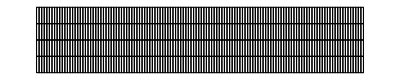

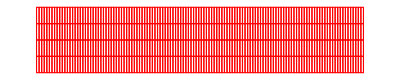

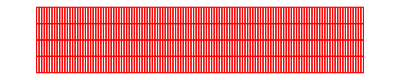

```mathematica
(*nyní jen vykreslíme*)
Show[BeamMesh["Wireframe"], ImageSize->Full]
Show[BeamMeshDeformed, ImageSize->Full]
Show[
BeamMesh["Wireframe"["ElementMeshDirective"->Directive[EdgeForm[GrayLevel[0.9]],FaceForm[]]]],
ElementMeshDeformation[BeamMesh,{uif,vif}, "ScalingFactor"->10]["Wireframe"["ElementMeshDirective"->Directive[EdgeForm[Red],FaceForm[]]]],
ImageSize->Full]
```

## Dubový trám se závažím

```mathematica
(*jediná věc co se změní bude parametr q*)
ClearAll["Global`*"]
Needs["NDSolve`FEM`"]
```

```mathematica
m=100 ;(*hmostnost závaží*)
L=0.3; (*místo, které zabírá*)
dens=650;
BeamLength= 10; 
BeamWidth = 0.25;
q=BeamWidth^2*dens*9.81;(*q=S*g*Rho=a^2*Rho*g*)
EE:= 11*10^9;
Izz=dens*BeamLength*BeamWidth^4/6;(*wikipedia->Izz=1/12*m*(sirka^2+vyska^2)*)
LoadDensity[X_]:=Piecewise[{{q, x<-L/2}, {q+m*9.81/L, -L/2≤x&&x≤L/2}, {q, L/2<x}}]
```

```mathematica
EulerBernoulliSolution = 
DSolve[
{
D[EE*Izz*D[y[X], X, X], X, X] == LoadDensity[X], 
y[-BeamLength/2]==0, 
y[BeamLength/2]==0, 
y'[-BeamLength/2]==0, 
y'[BeamLength/2]==0
}, 
y, 
X];
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
DisplacementEulerBernoulli[X_, Y_]:= {-Y*Sin[ArcTan[y'[X]]],y[X] + Y*(Cos[ArcTan[y'[X]]]-1)  }  /. EulerBernoulliSolution
u=Function[{X,Y},DisplacementEulerBernoulli[X, Y][[1]][[1]]]; 
v=Function[{X,Y},DisplacementEulerBernoulli[X, Y][[1]][[2]]]; 
BeamMesh = ToElementMesh[Rectangle[{-BeamLength/2, -BeamWidth/2}, {BeamLength/2, BeamWidth/2}]];
uif=ElementMeshInterpolation[{BeamMesh},u@@@BeamMesh["Coordinates"]]; 
vif=ElementMeshInterpolation[{BeamMesh},v@@@BeamMesh["Coordinates"]];
BeamMeshDeformed = ElementMeshDeformation[BeamMesh,{uif,vif}, "ScalingFactor"->10]["Wireframe"["ElementMeshDirective"->Directive[EdgeForm[Red],FaceForm[]]]]; 
BeamMeshDeformed = ElementMeshDeformation[BeamMesh,{uif,vif}, "ScalingFactor"->10]["Wireframe"["ElementMeshDirective"->Directive[EdgeForm[Red],FaceForm[]]]];
```

ElementMeshInterpolation::umn: Interpolation on unstructured grids is currently only supported for machine numbers.

```mathematica
Show[BeamMesh["Wireframe"], ImageSize->Full];
Show[BeamMeshDeformed, ImageSize->Full];
Show[
BeamMesh["Wireframe"["ElementMeshDirective"->Directive[EdgeForm[GrayLevel[0.9]],FaceForm[]]]],
ElementMeshDeformation[BeamMesh,{uif,vif}, "ScalingFactor"->10]["Wireframe"["ElementMeshDirective"->Directive[EdgeForm[Red],FaceForm[]]]],
ImageSize->Full];
```

Show::gtype: NDSolve`FEM`ElementMeshVisualizationDump`iElementMeshDeformation[ElementMesh[{{-5.,-0.125},{-5.,-0.0625},{-5.,0.},{-5.,0.0625},{-5.,0.125},{-4.92126,-0.125},{-4.92126,-0.0625},{-4.92126,0.},{-4.92126,0.0625},{-4.92126,0.125},«1777»},{QuadElement[{{1,6,7,2,641,642,643,644},{2,7,8,3,643,645,646,647},«7»,{12,17,18,13,665,666,667,657},«498»}]},{«1»},{PointElement[{{1},{2},{3},{4},{5},{6},{10},{11},{15},{16},«514»},{1,2,2,2,3,1,3,1,3,1,«514»}]}],«2»,Sca…ctor→10] is not a type of graphics.

Show::gcomb: Could not combine the graphics objects in Show[,NDSolve`FEM`ElementMeshVisualizationDump`iElementMeshDeformation[«1»][Wireframe[ElementMeshDirective→Directive[EdgeForm[RGBColor[1, 0, 0]],FaceForm[]]]],ImageSize→Full].